{q→0.631322,m→0.700897}

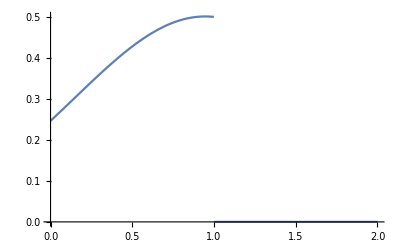

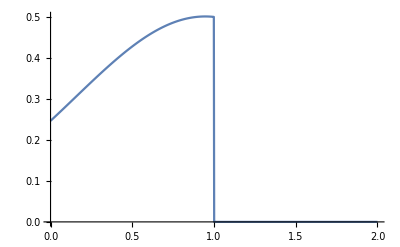

histvecth.csv

xvecth.csv

```mathematica
Clear["Global`*"];
(*Solving for the delta *)
r = 3.4;
sigma = 0.2;
mu =0.6;
startq = (1-1/r)^2+0.5;
startm = (1-1/r)+0.1;
sol = FindRoot[{(√q sigma (√q √((-1+mu)^2/(q sigma^2)) sigma+(-1+mu) Erf[(1+(-1+m) mu r)/(√2 √q r sigma)]))/(2 (-1+mu)^2 √((q sigma^2)/(-1+mu)^2))+1/(2 (1-mu)^3 √(2 π) r^2 √((q sigma^2)/(-1+mu)^2))√q sigma (-2 ⅇ^(-(1+(-1+m) mu r)^2/(2 q r^2 sigma^2)) √q r (1+(-1+m) mu r) sigma+4 ⅇ^(-(1+(-1+m) mu r)^2/(2 q r^2 sigma^2)) √q r (1+(-1+m mu) r) sigma-2 ⅇ^(-(1+(-1+m mu) r)^2/(2 q r^2 sigma^2)) √q r (1+(-1+m mu) r) sigma+√(2 π) (1+(-1+m mu) r)^2 Erf[(1+(-1+m) mu r)/(√2 √q r sigma)]+√(2 π) q r^2 sigma^2 Erf[(1+(-1+m) mu r)/(√2 √q r sigma)]-√(2 π) (1+(-1+m mu) r)^2 Erf[(1+(-1+m mu) r)/(√2 √q r sigma)]-√(2 π) q r^2 sigma^2 Erf[(1+(-1+m mu) r)/(√2 √q r sigma)])==q,(√q sigma (√q √((-1+mu)^2/(q sigma^2)) sigma+(-1+mu) Erf[(1+(-1+m) mu r)/(√2 √q r sigma)]))/(2 (-1+mu)^2 √((q sigma^2)/(-1+mu)^2))+(√((q sigma^2)/(-1+mu)^2) (2 (-ⅇ^(-(1+(-1+m) mu r)^2/(2 q r^2 sigma^2))+ⅇ^(-(1-r+m mu r)^2/(2 q r^2 sigma^2))) √q r sigma-√(2 π) (1+(-1+m mu) r) Erf[(1+(-1+m) mu r)/(√2 √q r sigma)]+√(2 π) (1-r+m mu r) Erf[(1-r+m mu r)/(√2 √q r sigma)]))/(2 √(2 π) √q r sigma)==m},{{q, startq},{m,startm}}]
q0 = q/.sol;
m0 = m/.sol;

f[x_]:= Exp[-(x-(1-1/r -mu m0)/(1-mu))^2/(2 sigma^2 q0/(1-mu)^2)]/Sqrt[2 Pi sigma^2 q0/(1-mu)^2]HeavisideTheta[1-x] ;


Plot[f[x], {x, 0,2}]
xmin = 0;
xmax = 2;
numx = 1000;
xvec = Table[x,{x,xmin,xmax,(xmax-xmin)/(numx-1)}];
histvec = f[xvec];
ListLinePlot[Transpose[{xvec,histvec}],PlotRange->All]

SetDirectory[NotebookDirectory[]];
Export["histvecth.csv",N[histvec]]
Export["xvecth.csv",N[xvec]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99824505334275412372045666042907896553515456616878509521484375}. NIntegrate obtained -125.535 and 93.0286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99824505334275412372045666042907896553515456616878509521484375}. NIntegrate obtained -125.929 and 92.882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99824505334275412372045666042907896553515456616878509521484375}. NIntegrate obtained -29.5332 and 19.5685 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-0.553854

-0.926026

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in myx near {myx} = {0.9996180180877353953889340176797162484945147298276424407958984375}. NIntegrate obtained 169815. and 54156.5 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in myx near {myx} = {0.993624608579271}. NIntegrate obtained 72681.3 and 57952.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in myx near {myx} = {0.987540325664247}. NIntegrate obtained 163136. and 149276. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

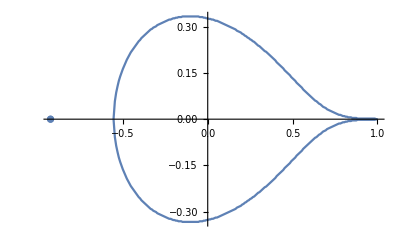

xvecjaccutoffmu.csv

yvecjaccutoffmu.csv

yvecellipsemu.csv

xvecellipsemu.csv

outlierloc.csv

```mathematica
Clear["Global`*"];

r = 3.4;
sigma = 0.2;
mu = 0.6;
startq = (1-1/r)^2+0.5;
startm = (1-1/r)+0.1;
sol = FindRoot[{(√q sigma (√q √((-1+mu)^2/(q sigma^2)) sigma+(-1+mu) Erf[(1+(-1+m) mu r)/(√2 √q r sigma)]))/(2 (-1+mu)^2 √((q sigma^2)/(-1+mu)^2))+1/(2 (1-mu)^3 √(2 π) r^2 √((q sigma^2)/(-1+mu)^2))√q sigma (-2 ⅇ^(-(1+(-1+m) mu r)^2/(2 q r^2 sigma^2)) √q r (1+(-1+m) mu r) sigma+4 ⅇ^(-(1+(-1+m) mu r)^2/(2 q r^2 sigma^2)) √q r (1+(-1+m mu) r) sigma-2 ⅇ^(-(1+(-1+m mu) r)^2/(2 q r^2 sigma^2)) √q r (1+(-1+m mu) r) sigma+√(2 π) (1+(-1+m mu) r)^2 Erf[(1+(-1+m) mu r)/(√2 √q r sigma)]+√(2 π) q r^2 sigma^2 Erf[(1+(-1+m) mu r)/(√2 √q r sigma)]-√(2 π) (1+(-1+m mu) r)^2 Erf[(1+(-1+m mu) r)/(√2 √q r sigma)]-√(2 π) q r^2 sigma^2 Erf[(1+(-1+m mu) r)/(√2 √q r sigma)])==q,(√q sigma (√q √((-1+mu)^2/(q sigma^2)) sigma+(-1+mu) Erf[(1+(-1+m) mu r)/(√2 √q r sigma)]))/(2 (-1+mu)^2 √((q sigma^2)/(-1+mu)^2))+(√((q sigma^2)/(-1+mu)^2) (2 (-ⅇ^(-(1+(-1+m) mu r)^2/(2 q r^2 sigma^2))+ⅇ^(-(1-r+m mu r)^2/(2 q r^2 sigma^2))) √q r sigma-√(2 π) (1+(-1+m mu) r) Erf[(1+(-1+m) mu r)/(√2 √q r sigma)]+√(2 π) (1-r+m mu r) Erf[(1-r+m mu r)/(√2 √q r sigma)]))/(2 √(2 π) √q r sigma)==m},{{q, startq},{m,startm}}];
q0 = q/.sol;
m0 = m/.sol;



eps = 0.001;
numom = 1000;
ommin = -1.1; 
ommax = 1.1;
omvec = Table[myom,{myom, ommin, ommax, (ommax - ommin)/(numom -1)}];
fvecout = Table[0,{myom, ommin, ommax, (ommax - ommin)/(numom -1)}];
fvecbulk = Table[0,{myom, ommin, ommax, (ommax - ommin)/(numom -1)}];

For[j= 1, j<numom+1, j++,
om= omvec[[j]];
phi =- (-Erf[(-1+r-m0 mu r)/(√2 √q0 r sigma)]+Erf[(-1+mu (r-m0 r))/(√2 √q0 r sigma)])/2;
achi = NIntegrate[((ⅇ^(-((1-mu)^2 (-(1-m mu-1/r)/(1-mu)+x)^2)/(2 q sigma^2)) (1-mu) (-(1-m mu-1/r)/(1-mu)+x))/(√(2 π) q sigma^2 √((q sigma^2)/(1-mu)^2))/.sol)r x/(om-1+ r(1-mu)x),{x,0,1}];
achi2 = NIntegrate[((ⅇ^(-((1-mu)^2 (-(1-m mu-1/r)/(1-mu)+x)^2)/(2 q sigma^2)) (1-mu) (-(1-m mu-1/r)/(1-mu)+x))/(√(2 π) q sigma^2 √((q sigma^2)/(1-mu)^2))/.sol)r x^2/(om-1+ r(1-mu)x),{x,0,1}];
aq =  NIntegrate[(Exp[-(x-(1-1/r -mu m )/(1-mu))^2/(2 sigma^2 q/(1-mu)^2)]/Sqrt[2 Pi sigma^2 q/(1-mu)^2]/.sol)r x^2/(om-1+ r(1-mu)x),{x,0,1}];
am=  NIntegrate[(Exp[-(x-(1-1/r -mu m )/(1-mu))^2/(2 sigma^2 q/(1-mu)^2)]/Sqrt[2 Pi sigma^2 q/(1-mu)^2]/.sol)r x/(om-1+ r(1-mu)x),{x,0,1}];



fvecout[[j]] = am/phi + sigma^2 achi aq/(phi(1-sigma^2 achi2)) +1/(mu phi);


(*fvecout[[j]] = NIntegrate[-r mu  Exp[-(myx-(1-1/r -mu m0)/(1-mu))^2/(2 sigma^2 q0/(1-mu)^2)]/Sqrt[2 Pi sigma^2 q0/(1-mu)^2]myx/(om +r(1-mu)myx -1),{myx, 0, 1}];*)
fvecbulk[[j]] = NIntegrate[sigma^2 Exp[-(myx-(1-1/r -mu m0)/(1-mu))^2/(2 sigma^2 q0/(1-mu)^2)]/Sqrt[2 Pi sigma^2 q0/(1-mu)^2] r^2myx^2/((1 - r(1-mu) myx - om)^2),{myx, 0, 1}];

];
nearest = Nearest[fvecbulk,1][[1]];
pos = Position[fvecbulk, nearest][[1,1]];
critom = omvec[[pos]]
nearest = Nearest[fvecout,0][[1]];
pos = Position[fvecout, nearest][[1,1]];
critomout= omvec[[pos]]


xmin = critom-0.001;
xmax =1.0;
numx = 200;
xvec = Table[s, {s, xmin, xmax, (xmax-xmin)/(numx-1)}];
crityvec = Table[s,{s, xmin, xmax, (xmax-xmin)/(numx-1)}];
crityvecapprox = Table[s,{s, xmin, xmax, (xmax-xmin)/(numx-1)}];
numy = 200;
ymin = 0; 
ymax =0.4;
yvec = Table[y,{y,ymin, ymax, (ymax - ymin)/(numy -1)}];





effinf  =1000;
eps = 0.0000001;
phi1 =(√q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2));
Monitor[For[j= 1, j<numx+1, j++,
x = xvec[[j]];
fvec = Table[y,{y,ymin, ymax, (ymax - ymin)/(numy -1)}];
fvecapprox = Table[y,{y,ymin, ymax, (ymax - ymin)/(numy -1)}];
For[i = 1, i<numy+1, i++,
y = yvec[[i]];

start =10.0;



fvec[[i]] = NIntegrate[sigma^2 Exp[-(myx-(1-1/r -mu m0)/(1-mu))^2/(2 sigma^2 q0/(1-mu)^2)]/Sqrt[2 Pi sigma^2 q0/(1-mu)^2] r^2myx^2/((1 - r (1-mu)myx - x)^2+y^2),{myx, 0, 1}];(* +  phi1 r^2sigma^2/((1 - r - x)^2+y^2);*)


];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
crityvec[[j]] = yvec[[pos]];
];,j];


plt1 = ListLinePlot[Transpose[{ xvec,crityvec}], PlotRange->All];
plt2 = ListLinePlot[Transpose[{ xvec,-crityvec}], PlotRange->All];
plt3 = ListPlot[{{critomout,0.0}}];
Show[plt2, plt1,plt3, PlotRange->All]
SetDirectory[NotebookDirectory[]];
Export["xvecjaccutoffmu.csv", xvec]
Export["yvecjaccutoffmu.csv", crityvec]

phi = NIntegrate[Exp[-(myx-(1-1/r -mu m0)/(1-mu))^2/(2 sigma^2 q0/(1-mu)^2)]/Sqrt[2 Pi sigma^2 q0/(1-mu)^2] ,{myx, 0, 1}];
xmin = -Sqrt[phi sigma^2];
xmax =Sqrt[phi sigma^2];
numx = 1000;
xvec = Table[s, {s, xmin, xmax, (xmax-xmin)/(numx-1)}];
yvecellipse = Sqrt[sigma^2 phi-xvec^2];
Export["yvecellipsemu.csv", yvecellipse]
Export["xvecellipsemu.csv", xvec]
Export["outlierloc.csv", critomout]
```

```mathematica
phi = NIntegrate[Exp[-(myx-(1-1/r -mu m0)/(1-mu))^2/(2 sigma^2 q0/(1-mu)^2)]/Sqrt[2 Pi sigma^2 q0/(1-mu)^2] ,{myx, 0, 1}];
xmin = -Sqrt[phi sigma^2];
xmax =Sqrt[phi sigma^2];
numx = 1000;
xvec = Table[s, {s, xmin, xmax, (xmax-xmin)/(numx-1)}];
yvecellipse = Sqrt[sigma^2 phi-xvec^2];
Export["yvecellipsemu.csv", yvecellipse]
Export["xvecellipsemu.csv", xvec]
Export["outlierloc.csv", critomout]
```

yvecellipsemu.csv

xvecellipsemu.csv

outlierloc.csv

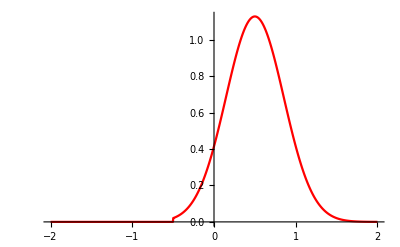

diaghistvecth.csv

diagxvecth.csv

```mathematica
Clear["Global`*"];

r = 1.5;
sigma = Sqrt[0.3];
start = (1-1/r)^2;
sol = FindRoot[(-ⅇ^(-(-1+1/r)^2/(2 q)) √q (-1+r) r (-2+sigma) sigma-ⅇ^(-1/(2 q r^2)) √q r sigma (-2+2 r+sigma)-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r)])/(√(2 π) r^2)+1/2 Erfc[1/(√2 √q r)]==q,{q, start}];

q0 = q/.sol;

px[x_]:= 1/Sqrt[2Pi sigma^2r^2q0] Exp[-(x-2+r)^2/(2 sigma^2 r^2q0)]HeavisideTheta[x-(1-r)] ;

plt1  = Plot[px[x_], {x, -2,2}];


xmin = -2;
xmax = 2;
numx = 1000;
xvec = Table[x,{x,xmin,xmax,(xmax-xmin)/(numx-1)}];
histvec = px[xvec];
plt2 =ListLinePlot[Transpose[{xvec,histvec}],PlotRange->All, PlotStyle->Red];
Show[plt1,plt2]

SetDirectory[NotebookDirectory[]];
Export["diaghistvecth.csv",N[histvec]]
Export["diagxvecth.csv",N[xvec]]
```

```mathematica
NIntegrate[px[x], {x,-Infinity, Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.497111}. NIntegrate obtained 0.997666 and 6.09883×10^-6 for the integral and error estimates.

0.997666

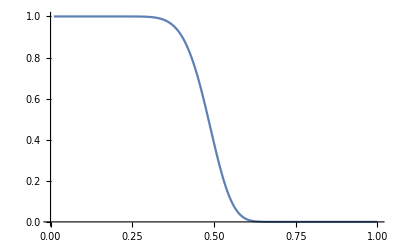

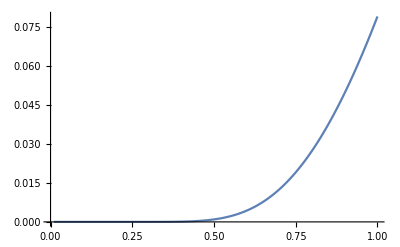

```mathematica
Clear["Global`*"];

gamma = 0;
mu = 0;
r = 1.5;
myn = 1000;

sigmamin = 0.1;
sigmamax =1.0;
numsigma= 1000;
sigmavec = Table[s, {s, sigmamin, sigmamax, (sigmamax-sigmamin)/(numsigma-1)}];
probvec = Table[s, {s, sigmamin, sigmamax, (sigmamax-sigmamin)/(numsigma-1)}];
fvec = Table[s, {s, sigmamin, sigmamax, (sigmamax-sigmamin)/(numsigma-1)}];




w0funct[mydelta_] := 0.5(1.0 + Erf[mydelta/Sqrt[2.0]]);
w1funct[mydelta_] := 0.5 (Sqrt[2.0/Pi]Exp[-mydelta^2/2.0]+ mydelta (1.0 + Erf[mydelta/Sqrt[2]]));
w2funct[mydelta_] := w0funct[mydelta] + mydelta w1funct[mydelta];


effinf  =1000;
eps = 0.0000001;
Monitor[For[j= 1, j<numsigma+1, j++,
sigma = sigmavec[[j]];


start =10.0;

(*Solving for the delta *)
sol = FindRoot[{sigma^2 ((1+gamma)( 0.5(1.0 + Erf[mydelta/Sqrt[2.0]])) + mydelta ( 0.5 (Sqrt[2.0/Pi]Exp[-mydelta^2/2.0]+ mydelta (1.0 + Erf[mydelta/Sqrt[2]]))))^2==( ( 0.5(1.0 + Erf[mydelta/Sqrt[2.0]])) + mydelta ( 0.5 (Sqrt[2.0/Pi]Exp[-mydelta^2/2.0]+ mydelta (1.0 + Erf[mydelta/Sqrt[2]]))))},{mydelta, start}];
{delta} = {mydelta} /.sol;
w0 = 0.5(1.0 + Erf[delta/Sqrt[2.0]]);
w1 = 0.5 (Sqrt[2.0/Pi]Exp[-delta^2/2.0]+ delta (1.0 + Erf[delta/Sqrt[2]]));
w2 = w0 + delta w1;

(*Phi is indepenent of mu*)
phi = w0;


(*Finds the fixed-point quantities*)
chi0 = w0 + gamma w0^2/w2;
m0 = (delta/w1 w2/(w2 + gamma w0)-mu)^(-1)*(1-1/r);
b = w2/(w2 + gamma w0);
q0 = (b m0 /(sigma w1))^2;

myf = 1/2 (1+Erf[(-3+r+m0 mu r)/(√2 √q0 r sigma)]);
probvec[[j]] = (1-myf)^myn;
fvec[[j]] = myf;

];,j];

plt1 = ListLinePlot[Transpose[{ sigmavec^2,probvec}], PlotRange->All]
plt1 = ListLinePlot[Transpose[{ sigmavec^2,fvec}], PlotRange->All]
(*SetDirectory[NotebookDirectory[]];
Export["sigmavec.csv",N[sigmavec]]
Export["probvecn1000.csv",N[probvec]]*)
```

```mathematica
Clear["Global`*"];Integrate[ Exp[-(myx-(1-1/r +mu m0))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0],{myx,2/r,Infinity }]
```

ConditionalExpression[(√q0 sigma (√q0 √(1/(q0 sigma^2)) sigma+Erf[(-3+r+m0 mu r)/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2)), ]

```mathematica
Simplify[(1+Erf[(-3+r+m0 mu r)/(√2 √q0 r sigma)])/2]
```

1/2 (1+Erf[(-3+r+m0 mu r)/(√2 √q0 r sigma)])

```mathematica
Clear["Global`*"];
Integrate[Exp[-z^2/2]/Sqrt[2Pi] (1-1/r + sigma Sqrt[q] z)^2, {z, (1/r-1)/(Sqrt[q]sigma), 1/(r sigma Sqrt[q])}] +Integrate[Exp[-z^2/2]/Sqrt[2Pi] , {z, 1/(r sigma Sqrt[q]), Infinity}]
```

(ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √q (-1+r) r sigma-ⅇ^(-1/(2 q r^2 sigma^2)) √q r (-1+2 r) sigma-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q sigma)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r sigma)])/(√(2 π) r^2)+1/2 Erfc[1/(√2 √q r sigma)]

```mathematica
Clear["Global`*"];
Integrate[ 1/Sqrt[2Pi q0 sigma^2] Exp[-(x-(1-1/r))^2/(2sigma^2q0)] ,{x, 1, Infinity}]
```

ConditionalExpression[(√q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2)), ]

```mathematica
Clear["Global`*"];
Solve[1 == r^2(1 - xi + etai)(1- r xi (1 - xi + etai)+ r xii), xi]
```

{{xi→(2 (r^3+etai r^3))/(3 r^3)-(2^(1/3) (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii))/(3 r^3 (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3))+1/(3 2^(1/3) r^3)(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3)},{xi→(2 (r^3+etai r^3))/(3 r^3)+((1+ⅈ √3) (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii))/(3 2^(2/3) r^3 (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3))-1/(6 2^(1/3) r^3)(1-ⅈ √3) (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3)},{xi→(2 (r^3+etai r^3))/(3 r^3)+((1-ⅈ √3) (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii))/(3 2^(2/3) r^3 (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3))-1/(6 2^(1/3) r^3)(1+ⅈ √3) (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3)}}

```mathematica
Simplify[(2 (r^3+etai r^3))/(3 r^3)-(2^(1/3) (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii))/(3 r^3 (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3))+1/(3 2^(1/3) r^3)(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3)]
```

1/(6 r^3)(4 (1+etai) r^3+(2 2^(1/3) r^5 (-3+r (1+2 etai+etai^2-3 xii)))/(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+√(r^12 ((27-9 (1+etai) r^2+(1+etai) r^3 (2+4 etai+2 etai^2-9 xii))^2-4 r^3 (-3+r (1+2 etai+etai^2-3 xii))^3))+9 r^9 xii+9 etai r^9 xii)^(1/3)+2^(2/3) (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+√(r^12 ((27-9 (1+etai) r^2+(1+etai) r^3 (2+4 etai+2 etai^2-9 xii))^2-4 r^3 (-3+r (1+2 etai+etai^2-3 xii))^3))+9 r^9 xii+9 etai r^9 xii)^(1/3))

```mathematica
Clear["Global`*"];
 Integrate[ myx^2 Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] ,{myx, 0, k}] +   Integrate[k^2  Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] ,{myx, k, Infinity}]
```

ConditionalExpression[(√q0 sigma ((2 ⅇ^(-(-1+1/r)^2/(2 q0 sigma^2)) √q0 (-1+r) sigma)/r-(2 ⅇ^(-(-1+k+1/r)^2/(2 q0 sigma^2)) √q0 (-1+r+k r) sigma)/r-(√(2 π) (-1+r)^2 Erf[(1-k-1/r)/(√2 √q0 sigma)])/r^2-√(2 π) q0 sigma^2 Erf[(-1+1/r)/(√2 √q0 sigma)]+√(2 π) q0 sigma^2 Erf[(-1+k+1/r)/(√2 √q0 sigma)]+(√(2 π) (-1+r)^2 Erf[(-1+r)/(√2 √q0 r sigma)])/r^2))/(2 √(2 π) √(q0 sigma^2))+(k^2 √q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[(1+(-1+k) r)/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2)), ]

```mathematica
Simplify[1/(2 √(2 π) √(q0 sigma^2))√q0 sigma ((2 ⅇ^(-(-1+1/r)^2/(2 q0 sigma^2)) √q0 (-1+r) sigma)/r-(2 ⅇ^(-(-1+k+1/r)^2/(2 q0 sigma^2)) √q0 (-1+r+k r) sigma)/r-(√(2 π) (-1+r)^2 Erf[(1-k-1/r)/(√2 √q0 sigma)])/r^2-√(2 π) q0 sigma^2 Erf[(-1+1/r)/(√2 √q0 sigma)]+√(2 π) q0 sigma^2 Erf[(-1+k+1/r)/(√2 √q0 sigma)]+(√(2 π) (-1+r)^2 Erf[(-1+r)/(√2 √q0 r sigma)])/r^2)+(k^2 √q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[(1+(-1+k) r)/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2))/.q0->q]
```

1/(2 √(q sigma^2))√q sigma ((ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √(2/π) √q (-1+r) sigma)/r-(ⅇ^(-(-1+k+1/r)^2/(2 q sigma^2)) √(2/π) √q (-1+r+k r) sigma)/r-((-1+r)^2 Erf[(1-k-1/r)/(√2 √q sigma)])/r^2-q sigma^2 Erf[(-1+1/r)/(√2 √q sigma)]+q sigma^2 Erf[(-1+k+1/r)/(√2 √q sigma)]+((-1+r)^2 Erf[(-1+r)/(√2 √q r sigma)])/r^2+k^2 (-1+√q √(1/(q sigma^2)) sigma+Erfc[(1+(-1+k) r)/(√2 √q r sigma)]))

```mathematica
Clear["Global`*"];
 Integrate[  Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] ,{myx, 0, 1}]
```

(√q0 sigma (-Erf[(-1+1/r)/(√2 √q0 sigma)]+Erf[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2))

```mathematica
Clear["Global`*"];
Simplify[Solve[(r-1)/(lambda-1 +(1-mu)(r-1))==-1/mu,lambda]]
```

{{lambda→2-r}}